```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_BITX/";
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
F2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

Make density out of cdf

-Graphics-

```mathematica
f2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[fNIG[x-z,α,β,μ1,δ1] fNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{6.01639,0.547637}

```mathematica
Timing[f2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{0.019353,0.3921}

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},n=Length[s];If[Length[x]==0,N[Length[Select[s,#1≤x&]]/(n+1)],Table[N[Length[Select[s,#1≤x⟦k⟧&]]/(n+1)],{k,1,Length[x]}]]]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITX Price | % Change | log return future | log return BITX
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 49175.9 | 3.54% | 0.0212907 | 0.0347737
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 47495.3 | -14.92% | -0.0904653 | -0.161541
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 55822.2 | -0.76% | -0.0196938 | -0.00759423
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 56247.7 | -2.14% | -0.131645 | -0.142883
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 64887. | 6.13% | 0.03685 | 0.0594724
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 61140.6 | -11.16% | -0.119603 | -0.118361
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 68822.9 | -2.54% | -0.042369 | -0.0256963
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 70614.3 | 2.20% | 0.018947 | 0.021806
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 69091.2 | -1.10% | -0.0359909 | 0.0107786)

```mathematica
data[[1,8]]
```

log return BITX

```mathematica
data[[1,7]]
```

log return future

```mathematica
tmp=Import[NotebookDirectory[] <> "data_bitx/" <> ToString[kk] <> "_parameters.csv"]
```

(2021-05-20
1.28713
0.115725
1.23024)

```mathematica
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
```

```mathematica
u=hatF[data[[2;;,8]]];
v=hatF[data[[2;;,7]]];
```

Attempt to determine LL from simulated data turns out to be very noisy

```mathematica
tmp=Import[NotebookDirectory[] <> "data_bitx/" <> ToString[kk] <> "_simulation.csv"];
```

```mathematica
tmp[[1;;10]]
```

(0.050439 | 0.0231795
0.0326793 | 0.0318994
0.405492 | 0.389492
0.467231 | 0.430491
0.99132 | 0.99098
0.935221 | 0.957461
0.960761 | 0.951661
0.50527 | 0.454751
0.720046 | 0.743125
0.99108 | 0.99216)

```mathematica
Dimensions[tmp]
```

{50000,2}

```mathematica
uv=tmp;
skd=SmoothKernelDistribution[uv];
```

-Graphics-

copula density

```mathematica
c2NIG[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{x,y},
x=NIGInv[u,α,β];
y=NIGInv[v,α,β];
f2NIG[x,y,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ] / (NIGPDF[x,α,β] NIGPDF[y,α,β])
]
```

```mathematica
Timing[c2NIG[0.5,0.1,5,0,0.2]]
```

{0.081954,0.998887}

-Graphics-

-Graphics-

```mathematica
c2NIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.773775,0.473979,0.882955,230.798,0.482931}

```mathematica
PDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{1.81072,3.99046,2.03549,3.89745,2.00486}

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
CNIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.668981,0.00324897,0.193945,0.00854791,0.815227}

```mathematica
CDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{0.666603,0.0100325,0.191242,0.00770657,0.812857}

```mathematica
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)]
```

386.151

```mathematica
%/Length[data]
```

1.28289

```mathematica
Timing[Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)]]
```

{20.7816,439.251}

```mathematica
%/Length[data]
```

{0.0690419,1.45931}

```mathematica
tLL={};
mLL={};
For[kk=0, kk<=80, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,8]]];
v=hatF[data[[2;;,7]]];
tmp=Import[NotebookDirectory[] <> "data_bitx/" <> ToString[kk] <> "_parameters.csv"];
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
ll=Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLL, ll];
AppendTo[mLL,mll];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.06375}. NIntegrate obtained 0.0257441 and 3.91872×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.23168}. NIntegrate obtained 0.0255121 and 7.24813×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {3.33928}. NIntegrate obtained 0.0227979 and 3.0618×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
tLL
```

{439.251,470.167,471.534,482.648,485.029,490.243,492.493,497.78,478.83,487.774,499.731,499.994,475.892,494.76,498.615,500.621,475.666,473.295,494.003,452.979,484.58,468.512,499.611,500.893,512.229,491.095,491.812,499.724,503.823,512.563,512.557,514.989,508.761,509.959,520.776,516.223,467.852,528.509,540.849,546.937,536.682,529.49,526.775,519.922,524.515,532.579,526.753,530.691,534.315,532.942,531.85,530.791,522.742,521.931,524.264,519.623,516.278,507.552,508.365,507.487,501.929,480.901,482.701,503.371,504.92,458.383,517.317,512.093,497.996,504.871,498.118,483.007,486.757,484.641,467.291,457.075,462.936,457.413,462.07,462.99,448.526}

```mathematica
mLL
```

{1.45931,1.56202,1.56656,1.60348,1.61139,1.62871,1.63619,1.65375,1.5908,1.62051,1.66023,1.66111,1.58104,1.64372,1.65653,1.66319,1.58029,1.57241,1.64121,1.50491,1.6099,1.55652,1.65984,1.6641,1.70176,1.63155,1.63393,1.66021,1.67383,1.70287,1.70285,1.71093,1.69024,1.69422,1.73015,1.71503,1.55433,1.75584,1.79684,1.81707,1.783,1.7591,1.75008,1.72732,1.74257,1.76937,1.75001,1.76309,1.77513,1.77057,1.76694,1.76342,1.73669,1.73399,1.74174,1.72632,1.71521,1.68622,1.68892,1.686,1.66754,1.59768,1.60366,1.67233,1.67747,1.52287,1.71866,1.7013,1.65447,1.67731,1.65488,1.60468,1.61713,1.6101,1.55246,1.51852,1.53799,1.51964,1.53512,1.53817,1.49012}

```mathematica
Export[NotebookDirectory[] <> "data_bitx_LL_NIG_bitx.csv", Prepend[{Range[0,80],tLL, mLL}ᵀ, {"", "LL", "mean LL"}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data_bitx_LL_NIG_bitx.csv

Gaussian copula

```mathematica
LLg[x_]:=Log[PDF[BinormalDistribution[{0,0}, {1,1}, ρ], x]]-Total[Log[PDF[NormalDistribution[],#]&/@x]]
```

```mathematica
ρ=0.9907220113152815;
ρ=0.9891018086831789;
```

```mathematica
tLLg={};
mLLg={};
For[kk=1, kk<=1, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLg[{InverseCDF[NormalDistribution[],#[[1]]],InverseCDF[NormalDistribution[],#[[2]]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLg, ll];
AppendTo[mLLg,mll];
]
```

```mathematica
tLLg
```

{365.689}

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Z=RandomVariate[NormalDistribution[],{100000,2}];
```

```mathematica
X=Z[[;;,1]];
Y=ρ Z[[;;,1]] + Sqrt[1-ρ^2] Z[[;;,2]];
```

```mathematica
U=hatF[X];
V=hatF[Y];
```

```mathematica
skd=SmoothKernelDistribution[{U,V}ᵀ];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
```

```mathematica
ll
```

382.909

Clayton copula

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

```mathematica
LLc[u_]:=Log[PDF[𝒟, u]]-Total[Log[#&/@u]]
```

```mathematica
c=40;
```

```mathematica
tLLc={};
mLLc={};
For[kk=18, kk<=18, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLc[{#[[1]],#[[2]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLc, ll];
AppendTo[mLLc,mll];
]
```

```mathematica
tLLc
```

{548.926}

```mathematica
mLLc
```

{1.82367}

```mathematica
Quantile[𝒟, {0.5, 0.5}]
```

Quantile[CopulaDistribution[{Clayton,1/40},{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{0.5,0.5}]

-Graphics-

```mathematica
ClaytonCDF[u_,v_]:=(u^-c+v^-c-1)^(-1/c)
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

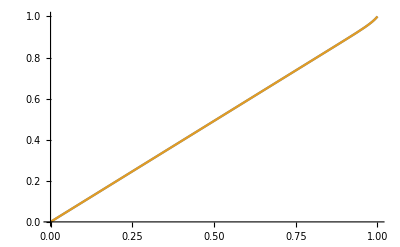

```mathematica
Plot[{CDF[𝒟, {u,u}],ClaytonCDF[u,u]}, {u,0,1}]
```

```mathematica
Simplify[ClaytonCDF[q,q]/q]
```

1/((2/q^40-1)^(1/40) q)

```mathematica
Simplify[CDF[𝒟,{q,q}]/q, Assumptions->0<q<1]
```

1/((2-q^40)^(1/40))

```mathematica
QD[q_?NumericQ]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
QD2[q_?NumericQ]:=
If[0<q≤0.5, ClaytonCDF[q,q]/q,(1-2q+ ClaytonCDF[q,q])/(1-q)]
```

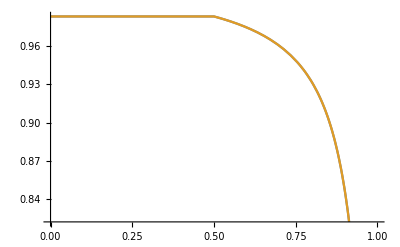

```mathematica
Plot[{QD[q],QD2[q]}, {q,0,1}]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
kk=18;
```

```mathematica
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

```mathematica
Clear[c, QD,𝒟]
```

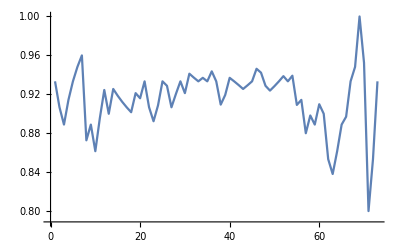

```mathematica
ListPlot[Table[QDemp[q, u, v], {q,0.05,0.95, 0.0125}],Joined->True]
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
QD[q_]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
target=Table[QDemp[q, u, v], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[target, KendallTau[u,v]];
target
```

{0.933333,0.933333,1.,0.933333,0.884563}

```mathematica
f= Table[QD[q], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[f, c/(c+2)]; (* Kendall's tau *)
Sqrt[Total[(target-f)^2]]
```

√((0.933333-20. (2 0.05^-c-1)^(-1/c))^2+(0.933333-10. (2 0.1^-c-1)^(-1/c))^2+(1.-10. ((2 0.9^-c-1)^(-1/c)-0.8))^2+(0.933333-20. ((2 0.95^-c-1)^(-1/c)-0.9))^2+(0.884563-c/(c+2))^2)

```mathematica
NMinimize[{Sqrt[Total[(target-f)^2]], c>0}, c]
```

{0.141561,{c→181.081}}

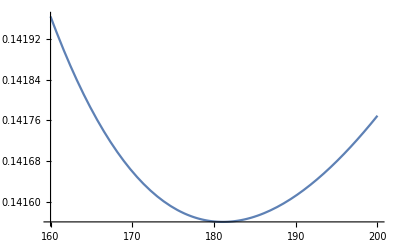

```mathematica
Plot[Sqrt[Total[(target-f)^2]], {c,160,200}]
```